```mathematica
Quit[]
```

```mathematica
NotebookDirectory[]
```

/home/riccardo/Documents/Fisica/Tesi/Processes/p-mm_2L_planar_massless_notr/ifdefinition/

## Input

```mathematica
<<"/home/riccardo/Programs/FeynArts/FeynArts/FeynArts.m";
<<"/home/riccardo/Programs/FormCalc/FormCalc-9.10/FormCalc.m";
Remove[q1];
Remove[q2];
<<"/home/riccardo/Programs/ABISS/ABISS/ABISS.m";
```

FeynArts 3.11 (25 Mar 2022)

by Hagen Eck, Sepp Kueblbeck, and Thomas Hahn

FormCalc 9.10 (30 Aug 2022)

by Thomas Hahn

+++++ ABISS` +++++
Version 1.0.0

Amplitudes Builder, Interference Solver and Simplifier

```mathematica
SetPath[NotebookDirectory[]];
process={F[3,{1,o}],-F[3,{1,o}]}->{F[2,{2}],-F[2,{2}]};
SetProcess[process];
```

```mathematica
GenerateInput[];
```

ABISS Warning: Input file /home/riccardo/Documents/Fisica/Tesi/Processes/p-mm_2L_planar_massless_notr/ifdefinition/input/kinematics.m already exist. It will NOT be overwritten.

ABISS Warning: Input file /home/riccardo/Documents/Fisica/Tesi/Processes/p-mm_2L_planar_massless_notr/ifdefinition/input/integral_families.m already exist. It will NOT be overwritten.

```mathematica
ImportInput[];
```

ABISS: Imported input file /home/riccardo/Documents/Fisica/Tesi/Processes/p-mm_2L_planar_massless_notr/ifdefinition/input/kinematics.m.

ABISS: Imported input file /home/riccardo/Documents/Fisica/Tesi/Processes/p-mm_2L_planar_massless_notr/ifdefinition/input/integral_families.m.

ABISS: Imported input file /home/riccardo/Documents/Fisica/Tesi/Processes/p-mm_2L_planar_massless_notr/ifdefinition/input/equivalence_classes.m

## Prop lists

## Amplitude Backup

```mathematica
myAmpBorn=<<(NotebookDirectory[]<>"../feynArts_amplitudes/BornAmplitudes.m");
myAmp1L=<<(NotebookDirectory[]<>"../feynArts_amplitudes/OneLoopAmplitudes.m");
myAmp2L=<<(NotebookDirectory[]<>"../feynArts_amplitudes/TwoLoopAmplitudes.m");
```

```mathematica
Print["Number of diagrams: ", {myAmpBorn,myAmp1L,myAmp2L}//Map[Length]]
```

Number of diagrams: {1,6,278}

Modellistica
analisi
aziende che cercano rpfili qualificati
avere un dottorato vuol dire dimostrare di essere in grado di sviluppare un pensiero scientifico e originale

## Interference

### Mass Options

```mathematica
normalMass={};
SetZeroMassParticles[normalMass]
```

```mathematica
zeroMass={mu->0,md->0,ms->0,me->0,mm->0};
SetZeroMassParticles[zeroMass]
```

```mathematica
(*myAmpBorn=myAmpBorn/.zeroOnShellMass;
myAmp1L=myAmp1L/.zeroOnShellMass;*)
```

### Computation

```mathematica
ImportInput[]
```

ABISS: Imported input file /home/riccardo/Documents/Fisica/Tesi/Processes/p-mm_2L_planar_massless_notr/ifdefinition/input/kinematics.m.

ABISS: Imported input file /home/riccardo/Documents/Fisica/Tesi/Processes/p-mm_2L_planar_massless_notr/ifdefinition/input/integral_families.m.

ABISS: Imported input file /home/riccardo/Documents/Fisica/Tesi/Processes/p-mm_2L_planar_massless_notr/ifdefinition/input/equivalence_classes.m

We want an estimate of the computational time

```mathematica
testFactor=FermionChain[NonCommutative[DiracSpinor[-FourMomentum[Incoming, 2], MU]], EL*NonCommutative[ChiralityProjector[1]]+EL*NonCommutative[ChiralityProjector[-1]],NonCommutative[DiracSpinor[FourMomentum[Incoming, 1], MU]]]*
 FermionChain[NonCommutative[DiracSpinor[FourMomentum[Outgoing, 1], MM]], EL*NonCommutative[ChiralityProjector[1]]+EL*NonCommutative[ChiralityProjector[-1]],NonCommutative[DiracSpinor[-FourMomentum[Outgoing, 2], MM]]]*PropagatorDenominator[FourMomentum[Outgoing,1]+FourMomentum[Outgoing,2],0]/EL^2
```

1/EL^2 DiracSpinor[-(p2),MU].(EL ChiralityProjector[-1]+EL ChiralityProjector[1]).DiracSpinor[p1,MU] DiracSpinor[k1,MM].(EL ChiralityProjector[-1]+EL ChiralityProjector[1]).DiracSpinor[-(k2),MM] 1/(k1+k2)^2

```mathematica
faDenominators=Cases[myAmp2L,FeynAmpDenominator[___],Infinity]
```

{FeynAmpDenominator[1/(-MH^2+(q1)^2),1/(-MM^2+(q2)^2),1/(-MM^2+(q1+k1)^2),1/(-MH^2+(q1+q2+k1)^2),1/(-MM^2+(q1-k2)^2),1/(-MM^2+(q2+k1+k2)^2)],FeynAmpDenominator[1/(-MZ^2+(q1)^2),1/(-MM^2+(q2)^2),1/(-MM^2+(q1+k1)^2),1/(-MH^2+(q1+q2+k1)^2),1/(-MM^2+(q1-k2)^2),1/(-MM^2+(q2+k1+k2)^2)],275,FeynAmpDenominator[1/(-MM^2+(q1)^2),1/(q2)^2,1/(-MW^2+(q1+q2)^2),1/(-MZ^2+(q1-k1)^2),1/(-MW^2+(q2-k2)^2),1/(-MW^2+(q1+q2-k1-k2)^2)]}
 |  |  |  |

```mathematica
Length[faDenominators]
```

278

```mathematica
plDenominators=Map[AmpSquare[#*testFactor,testFactor]&,faDenominators];
```

```mathematica
sm=Table[<<(NotebookDirectory[]<>"../../p-mm_2L_planar_massless_notr_old/interferences/Contribution_"<>ToString[i]<>"_1.m"),{i,278}];
```

```mathematica
notnullList={};
Do[
If[sm[[i]]=!=0,notnullList=Append[notnullList,i]]
,{i,1,278}]
notnullList
Length[notnullList]
```

{101,102,103,104,105,119,120,121,122,123,124,125,126,127,128,149,150,151,152,153,154,155,156,157,158,159,160,161,162,163,164,165,166,167,168,169,170,171,194,195,196,197,198,199,200,201,202,203,204,205,206,207,208,209,210,211,212,225,226,227,228,229,230,231,232,233,234,257,258,259,260,275,276,277,278}

75

```mathematica
pl=Map[plDenominators[[#]]&,notnullList];
```

```mathematica
Length[pl]
```

8

```mathematica
AmpSquare[testFactor,testFactor]
```

1

```mathematica
AmpSquare[myAmp2L[[1]],myAmpBorn[[1]]]//Simplify
```

0

## Shift

## Shift and Save

```mathematica
ImportInput[]
```

ABISS: Imported input file /home/riccardo/Documents/Fisica/Tesi/Processes/p-mm_2L_planar_massless_notr/ifdefinition/input/kinematics.m.

ABISS: Imported input file /home/riccardo/Documents/Fisica/Tesi/Processes/p-mm_2L_planar_massless_notr/ifdefinition/input/integral_families.m.

ABISS Warning: Overwritten file /home/riccardo/Documents/Fisica/Tesi/Processes/p-mm_2L_planar_massless_notr/ifdefinition/input/equivalence_classes.m

```mathematica
l=1;
(*ExtractFamily[sm[[l]]/.ShiftToIntegralFamily[sm[[l]]]]*)
ShiftToIntegralFamily[pl[[l]]]
extractKiraProp[pl[[l]]]
extractMomenta[pl[[l]]]
```

{{q1→q1,q2→q2}}

1

{}

```mathematica
ShiftToIntegralFamily[pl[[2]]]
```

{}

```mathematica
pl[[9]]
```

PropList[KiraPropagator[q1,0],KiraPropagator[p3+q1,mz],KiraPropagator[-p1-p2+p3+q1,0],KiraPropagator[q2,mw],KiraPropagator[p1+p2+q2,mw],KiraPropagator[p3+q1+q2,mw]]

```mathematica
plSort=SortBy[pl,numberOfMasses];
```

```mathematica
pl[[1]]
```

PropList[KiraPropagator[q1,0],KiraPropagator[p3+q1,0],KiraPropagator[-p1-p2+p3+q1,0],KiraPropagator[q2,0],KiraPropagator[p1+p2+q2,0],KiraPropagator[p3+q1+q2,0]]

```mathematica
numberOfMasses[pl[[2]]]
```

1

```mathematica
plByMass={};
Do[
If[numberOfMasses[pl[[i]]]===4,plByMass=Append[plByMass,pl[[i]]]]
,{i,Length[pl]}]
plByMass
```

{PropList[KiraPropagator[q1,0],KiraPropagator[-p3+q1,mw],KiraPropagator[q2,0],KiraPropagator[-p1-p2+p3+q2,mz],KiraPropagator[q1+q2,mw],KiraPropagator[-p1-p2+q1+q2,mw]],PropList[KiraPropagator[q1,0],KiraPropagator[-p3+q1,mz],KiraPropagator[q2,0],KiraPropagator[-p1-p2+p3+q2,mw],KiraPropagator[q1+q2,mw],KiraPropagator[-p1-p2+q1+q2,mw]]}

```mathematica
ImportInput[]
Do[If[ShiftToIntegralFamily[plByMass[[i]]]==={},Print[i," ",plByMass[[i]]],Print[ShiftToIntegralFamily[plByMass[[i]]]]],{i,1,Length[plByMass]}]
```

ABISS: Imported input file /home/riccardo/Documents/Fisica/Tesi/Processes/p-mm_2L_planar_massless_notr/ifdefinition/input/kinematics.m.

ABISS: Imported input file /home/riccardo/Documents/Fisica/Tesi/Processes/p-mm_2L_planar_massless_notr/ifdefinition/input/integral_families.m.

ABISS Warning: Overwritten file /home/riccardo/Documents/Fisica/Tesi/Processes/p-mm_2L_planar_massless_notr/ifdefinition/input/equivalence_classes.m

{{p1→p1,p2→p2,p3→p3,q1→q1,q2→q2}}

{{p1→p2,p2→p1,p3→p1+p2-p3,q1→q2,q2→q1}}

```mathematica
Do[If[ShiftToIntegralFamily[pl[[i]]]=!={},Print[i," ",ShiftToIntegralFamily[pl[[i]]]]],{i,1,Length[pl]}]
```

1 {{p1→p1,p2→p2,p3→p3,q1→q1,q2→q2}}

2 {{p1→p2,p2→p1,p3→p1+p2-p3,q1→-q1,q2→-p1-p2-q2}}

3 {{p1→p1+p2-p3,p2→p3,p3→p2,q1→p1+q2,q2→-p1-p2+p3+q1}}

4 {{p1→p2,p2→p1,p3→p1+p2-p3,q1→-q1,q2→-p1-p2-q2}}

5 {{p1→p2,p2→p1,p3→p1+p2-p3,q1→-q1,q2→-p1-p2-q2}}

6 {{p1→p2,p2→p1,p3→p1+p2-p3,q1→-q1,q2→-p1-p2-q2}}

7 {{p1→p2,p2→p1,p3→p1+p2-p3,q1→-q1,q2→-p1-p2-q2}}

8 {{p1→p1,p2→p2,p3→p3,q1→q1,q2→q2}}

9 {{p1→p2,p2→p1,p3→p1+p2-p3,q1→-q1,q2→-p1-p2-q2}}

10 {{p1→p2,p2→p1,p3→p1+p2-p3,q1→-q1,q2→-p1-p2-q2}}

11 {{p1→p1,p2→p2,p3→p3,q1→q1,q2→q2}}

12 {{p1→p2,p2→p1,p3→p1+p2-p3,q1→-q1,q2→-p1-p2-q2}}

13 {{p1→p2,p2→p1,p3→p1+p2-p3,q1→-q1,q2→-p1-p2-q2}}

14 {{p1→p1+p2-p3,p2→p3,p3→p2,q1→p1+q2,q2→-p1-p2+p3+q1}}

15 {{p1→p1+p2-p3,p2→p3,p3→p2,q1→p1+q2,q2→-p1-p2+p3+q1}}

16 {{p1→p2,p2→p1,p3→p1+p2-p3,q1→-q1,q2→-p1-p2-q2}}

17 {{p1→p2,p2→p1,p3→p1+p2-p3,q1→-q1,q2→-p1-p2-q2}}

18 {{p1→p2,p2→p1,p3→p1+p2-p3,q1→-q1,q2→-p1-p2-q2}}

19 {{p1→p2,p2→p1,p3→p1+p2-p3,q1→-q1,q2→-p1-p2-q2}}

20 {{p1→p1,p2→p2,p3→p3,q1→q1,q2→q2}}

21 {{p1→p2,p2→p1,p3→p1+p2-p3,q1→-q1,q2→-p1-p2-q2}}

22 {{p1→p2,p2→p1,p3→p1+p2-p3,q1→-q1,q2→-p1-p2-q2}}

23 {{p1→p1,p2→p2,p3→p3,q1→q1,q2→q2}}

24 {{p1→p1,p2→p2,p3→p3,q1→q1,q2→q2}}

25 {{p1→p2,p2→p1,p3→p1+p2-p3,q1→-q1,q2→-p1-p2-q2}}

26 {{p1→p2,p2→p1,p3→p1+p2-p3,q1→-q1,q2→-p1-p2-q2}}

27 {{p1→p1,p2→p2,p3→p3,q1→q1,q2→q2}}

28 {{p1→p2,p2→p1,p3→p1+p2-p3,q1→-q1,q2→-p1-p2-q2}}

29 {{p1→p2,p2→p1,p3→p1+p2-p3,q1→-q1,q2→-p1-p2-q2}}

30 {{p1→p2,p2→p1,p3→p1+p2-p3,q1→-q1,q2→-p1-p2-q2}}

31 {{p1→p2,p2→p1,p3→p1+p2-p3,q1→-q1,q2→-p1-p2-q2}}

32 {{p1→p1+p2-p3,p2→p3,p3→p2,q1→p1+q2,q2→-p1-p2+p3+q1}}

33 {{p1→p1+p2-p3,p2→p3,p3→p2,q1→p1+q2,q2→-p1-p2+p3+q1}}

34 {{p1→p1+p2-p3,p2→p3,p3→p2,q1→p1+q2,q2→-p1-p2+p3+q1}}

35 {{p1→p1+p2-p3,p2→p3,p3→p2,q1→p1+q2,q2→-p1-p2+p3+q1}}

36 {{p1→p2,p2→p1,p3→p1+p2-p3,q1→-q1,q2→-p1-p2-q2}}

37 {{p1→p2,p2→p1,p3→p1+p2-p3,q1→-q1,q2→-p1-p2-q2}}

38 {{p1→p2,p2→p1,p3→p1+p2-p3,q1→-q1,q2→-p1-p2-q2}}

39 {{p1→p2,p2→p1,p3→p1+p2-p3,q1→-q1,q2→-p1-p2-q2}}

40 {{p1→p2,p2→p1,p3→p1+p2-p3,q1→-q1,q2→-p1-p2-q2}}

41 {{p1→p1,p2→p2,p3→p3,q1→q1,q2→q2}}

42 {{p1→p2,p2→p1,p3→p1+p2-p3,q1→-q1,q2→-p1-p2-q2}}

43 {{p1→p2,p2→p1,p3→p1+p2-p3,q1→-q1,q2→-p1-p2-q2}}

44 {{p1→p1,p2→p2,p3→p3,q1→q1,q2→q2}}

45 {{p1→p2,p2→p1,p3→p1+p2-p3,q1→-q1,q2→-p1-p2-q2}}

46 {{p1→p2,p2→p1,p3→p1+p2-p3,q1→-q1,q2→-p1-p2-q2}}

47 {{p1→p1+p2-p3,p2→p3,p3→p2,q1→p1+q2,q2→-p1-p2+p3+q1}}

48 {{p1→p1+p2-p3,p2→p3,p3→p2,q1→p1+q2,q2→-p1-p2+p3+q1}}

49 {{p1→p2,p2→p1,p3→p1+p2-p3,q1→-q1,q2→-p1-p2-q2}}

50 {{p1→p2,p2→p1,p3→p1+p2-p3,q1→-q1,q2→-p1-p2-q2}}

51 {{p1→p1,p2→p2,p3→p3,q1→q1,q2→q2}}

52 {{p1→p2,p2→p1,p3→p1+p2-p3,q1→-q1,q2→-p1-p2-q2}}

53 {{p1→p2,p2→p1,p3→p1+p2-p3,q1→-q1,q2→-p1-p2-q2}}

54 {{p1→p1,p2→p2,p3→p3,q1→q1,q2→q2}}

55 {{p1→p2,p2→p1,p3→p1+p2-p3,q1→-q1,q2→-p1-p2-q2}}

56 {{p1→p2,p2→p1,p3→p1+p2-p3,q1→-q1,q2→-p1-p2-q2}}

57 {{p1→p1+p2-p3,p2→p3,p3→p2,q1→p1+q2,q2→-p1-p2+p3+q1}}

58 {{p1→p2,p2→p1,p3→p1+p2-p3,q1→-q1,q2→-p1-p2-q2}}

59 {{p1→p2,p2→p1,p3→p1+p2-p3,q1→-q1,q2→-p1-p2-q2}}

60 {{p1→p1,p2→p2,p3→p3,q1→q1,q2→q2}}

61 {{p1→p2,p2→p1,p3→p1+p2-p3,q1→-q1,q2→-p1-p2-q2}}

62 {{p1→p2,p2→p1,p3→p1+p2-p3,q1→-q1,q2→-p1-p2-q2}}

63 {{p1→p1,p2→p2,p3→p3,q1→q1,q2→q2}}

64 {{p1→p2,p2→p1,p3→p1+p2-p3,q1→-q1,q2→-p1-p2-q2}}

65 {{p1→p2,p2→p1,p3→p1+p2-p3,q1→-q1,q2→-p1-p2-q2}}

66 {{p1→p1+p2-p3,p2→p3,p3→p2,q1→p1+q2,q2→-p1-p2+p3+q1}}

67 {{p1→p1+p2-p3,p2→p3,p3→p2,q1→p1+q2,q2→-p1-p2+p3+q1}}

68 {{p1→p1,p2→p2,p3→p3,q1→q1,q2→q2}}

69 {{p1→p1,p2→p2,p3→p3,q1→q1,q2→q2}}

70 {{p1→p2,p2→p1,p3→p1+p2-p3,q1→p1+p2-p3-q2,q2→p3-q1}}

71 {{p1→p2,p2→p1,p3→p1+p2-p3,q1→p1+p2-p3-q2,q2→p3-q1}}

72 {{p1→p1,p2→p2,p3→p3,q1→q1,q2→q2}}

73 {{p1→p2,p2→p1,p3→p1+p2-p3,q1→q2,q2→q1}}

74 {{p1→p1,p2→p2,p3→p3,q1→q1,q2→q2}}

75 {{p1→p2,p2→p1,p3→p1+p2-p3,q1→q2,q2→q1}}

```mathematica
Do[
ShiftAndSave[i,j];
,{i,1,278},{j,1}]
```

ABISS: Integral family {{B1, {0}}} already recognised for /home/riccardo/Documents/Fisica/Tesi/Processes/p-mm_2L_planar_massless_notr/interferences/Contribution_101_1.m.

ABISS: Integral family {{B5, {mz}}} already recognised for /home/riccardo/Documents/Fisica/Tesi/Processes/p-mm_2L_planar_massless_notr/interferences/Contribution_102_1.m.

ABISS: Integral family {{B6, {mz}}} already recognised for /home/riccardo/Documents/Fisica/Tesi/Processes/p-mm_2L_planar_massless_notr/interferences/Contribution_103_1.m.

ABISS: Integral family {{B7, {mz}}} already recognised for /home/riccardo/Documents/Fisica/Tesi/Processes/p-mm_2L_planar_massless_notr/interferences/Contribution_104_1.m.

ABISS: Integral family {{B7, {mw}}} already recognised for /home/riccardo/Documents/Fisica/Tesi/Processes/p-mm_2L_planar_massless_notr/interferences/Contribution_105_1.m.

ABISS: Integral family {{B8, {mw}}} already recognised for /home/riccardo/Documents/Fisica/Tesi/Processes/p-mm_2L_planar_massless_notr/interferences/Contribution_119_1.m.

ABISS: Integral family {{B8, {mw}}} already recognised for /home/riccardo/Documents/Fisica/Tesi/Processes/p-mm_2L_planar_massless_notr/interferences/Contribution_120_1.m.

ABISS: Integral family {{B9, {mw, mz}}} already recognised for /home/riccardo/Documents/Fisica/Tesi/Processes/p-mm_2L_planar_massless_notr/interferences/Contribution_121_1.m.

ABISS: Integral family {{B10, {mw, mz}}} already recognised for /home/riccardo/Documents/Fisica/Tesi/Processes/p-mm_2L_planar_massless_notr/interferences/Contribution_122_1.m.

ABISS: Integral family {{B10, {mw, mz}}} already recognised for /home/riccardo/Documents/Fisica/Tesi/Processes/p-mm_2L_planar_massless_notr/interferences/Contribution_123_1.m.

ABISS: Integral family {{B9, {mw, mz}}} already recognised for /home/riccardo/Documents/Fisica/Tesi/Processes/p-mm_2L_planar_massless_notr/interferences/Contribution_124_1.m.

ABISS: Integral family {{B11, {mw, mz}}} already recognised for /home/riccardo/Documents/Fisica/Tesi/Processes/p-mm_2L_planar_massless_notr/interferences/Contribution_125_1.m.

ABISS: Integral family {{B11, {mw, mz}}} already recognised for /home/riccardo/Documents/Fisica/Tesi/Processes/p-mm_2L_planar_massless_notr/interferences/Contribution_126_1.m.

ABISS: Integral family {{B13, {mw, mh}}} already recognised for /home/riccardo/Documents/Fisica/Tesi/Processes/p-mm_2L_planar_massless_notr/interferences/Contribution_127_1.m.

ABISS: Integral family {{B13, {mw, mz}}} already recognised for /home/riccardo/Documents/Fisica/Tesi/Processes/p-mm_2L_planar_massless_notr/interferences/Contribution_128_1.m.

ABISS: Integral family {{B8, {mw}}} already recognised for /home/riccardo/Documents/Fisica/Tesi/Processes/p-mm_2L_planar_massless_notr/interferences/Contribution_149_1.m.

ABISS: Integral family {{B8, {mw}}} already recognised for /home/riccardo/Documents/Fisica/Tesi/Processes/p-mm_2L_planar_massless_notr/interferences/Contribution_150_1.m.

ABISS: Integral family {{B8, {mw}}} already recognised for /home/riccardo/Documents/Fisica/Tesi/Processes/p-mm_2L_planar_massless_notr/interferences/Contribution_151_1.m.

ABISS: Integral family {{B8, {mw}}} already recognised for /home/riccardo/Documents/Fisica/Tesi/Processes/p-mm_2L_planar_massless_notr/interferences/Contribution_152_1.m.

ABISS: Integral family {{B9, {mw, mz}}} already recognised for /home/riccardo/Documents/Fisica/Tesi/Processes/p-mm_2L_planar_massless_notr/interferences/Contribution_153_1.m.

ABISS: Integral family {{B10, {mw, mz}}} already recognised for /home/riccardo/Documents/Fisica/Tesi/Processes/p-mm_2L_planar_massless_notr/interferences/Contribution_154_1.m.

ABISS: Integral family {{B10, {mw, mz}}} already recognised for /home/riccardo/Documents/Fisica/Tesi/Processes/p-mm_2L_planar_massless_notr/interferences/Contribution_155_1.m.

ABISS: Integral family {{B9, {mw, mz}}} already recognised for /home/riccardo/Documents/Fisica/Tesi/Processes/p-mm_2L_planar_massless_notr/interferences/Contribution_156_1.m.

ABISS: Integral family {{B9, {mw, mz}}} already recognised for /home/riccardo/Documents/Fisica/Tesi/Processes/p-mm_2L_planar_massless_notr/interferences/Contribution_157_1.m.

ABISS: Integral family {{B10, {mw, mz}}} already recognised for /home/riccardo/Documents/Fisica/Tesi/Processes/p-mm_2L_planar_massless_notr/interferences/Contribution_158_1.m.

ABISS: Integral family {{B10, {mw, mz}}} already recognised for /home/riccardo/Documents/Fisica/Tesi/Processes/p-mm_2L_planar_massless_notr/interferences/Contribution_159_1.m.

ABISS: Integral family {{B9, {mw, mz}}} already recognised for /home/riccardo/Documents/Fisica/Tesi/Processes/p-mm_2L_planar_massless_notr/interferences/Contribution_160_1.m.

ABISS: Integral family {{B11, {mw, mz}}} already recognised for /home/riccardo/Documents/Fisica/Tesi/Processes/p-mm_2L_planar_massless_notr/interferences/Contribution_161_1.m.

ABISS: Integral family {{B11, {mw, mz}}} already recognised for /home/riccardo/Documents/Fisica/Tesi/Processes/p-mm_2L_planar_massless_notr/interferences/Contribution_162_1.m.

ABISS: Integral family {{B11, {mw, mz}}} already recognised for /home/riccardo/Documents/Fisica/Tesi/Processes/p-mm_2L_planar_massless_notr/interferences/Contribution_163_1.m.

ABISS: Integral family {{B11, {mw, mz}}} already recognised for /home/riccardo/Documents/Fisica/Tesi/Processes/p-mm_2L_planar_massless_notr/interferences/Contribution_164_1.m.

ABISS: Integral family {{B12, {mw}}} already recognised for /home/riccardo/Documents/Fisica/Tesi/Processes/p-mm_2L_planar_massless_notr/interferences/Contribution_165_1.m.

ABISS: Integral family {{B13, {mw, mz}}} already recognised for /home/riccardo/Documents/Fisica/Tesi/Processes/p-mm_2L_planar_massless_notr/interferences/Contribution_166_1.m.

ABISS: Integral family {{B12, {mw}}} already recognised for /home/riccardo/Documents/Fisica/Tesi/Processes/p-mm_2L_planar_massless_notr/interferences/Contribution_167_1.m.

ABISS: Integral family {{B13, {mw, mz}}} already recognised for /home/riccardo/Documents/Fisica/Tesi/Processes/p-mm_2L_planar_massless_notr/interferences/Contribution_168_1.m.

ABISS: Integral family {{B2, {mw}}} already recognised for /home/riccardo/Documents/Fisica/Tesi/Processes/p-mm_2L_planar_massless_notr/interferences/Contribution_169_1.m.

ABISS: Integral family {{B15, {mz, mw}}} already recognised for /home/riccardo/Documents/Fisica/Tesi/Processes/p-mm_2L_planar_massless_notr/interferences/Contribution_170_1.m.

ABISS: Integral family {{B14, {mw}}} already recognised for /home/riccardo/Documents/Fisica/Tesi/Processes/p-mm_2L_planar_massless_notr/interferences/Contribution_171_1.m.

ABISS: Integral family {{B8, {mw}}} already recognised for /home/riccardo/Documents/Fisica/Tesi/Processes/p-mm_2L_planar_massless_notr/interferences/Contribution_194_1.m.

ABISS: Integral family {{B8, {mw}}} already recognised for /home/riccardo/Documents/Fisica/Tesi/Processes/p-mm_2L_planar_massless_notr/interferences/Contribution_195_1.m.

ABISS: Integral family {{B9, {mw, mz}}} already recognised for /home/riccardo/Documents/Fisica/Tesi/Processes/p-mm_2L_planar_massless_notr/interferences/Contribution_196_1.m.

ABISS: Integral family {{B10, {mw, mz}}} already recognised for /home/riccardo/Documents/Fisica/Tesi/Processes/p-mm_2L_planar_massless_notr/interferences/Contribution_197_1.m.

ABISS: Integral family {{B10, {mw, mz}}} already recognised for /home/riccardo/Documents/Fisica/Tesi/Processes/p-mm_2L_planar_massless_notr/interferences/Contribution_198_1.m.

ABISS: Integral family {{B9, {mw, mz}}} already recognised for /home/riccardo/Documents/Fisica/Tesi/Processes/p-mm_2L_planar_massless_notr/interferences/Contribution_199_1.m.

ABISS: Integral family {{B11, {mw, mz}}} already recognised for /home/riccardo/Documents/Fisica/Tesi/Processes/p-mm_2L_planar_massless_notr/interferences/Contribution_200_1.m.

ABISS: Integral family {{B11, {mw, mz}}} already recognised for /home/riccardo/Documents/Fisica/Tesi/Processes/p-mm_2L_planar_massless_notr/interferences/Contribution_201_1.m.

ABISS: Integral family {{B12, {mw}}} already recognised for /home/riccardo/Documents/Fisica/Tesi/Processes/p-mm_2L_planar_massless_notr/interferences/Contribution_202_1.m.

ABISS: Integral family {{B13, {mw, mz}}} already recognised for /home/riccardo/Documents/Fisica/Tesi/Processes/p-mm_2L_planar_massless_notr/interferences/Contribution_203_1.m.

ABISS: Integral family {{B8, {mw}}} already recognised for /home/riccardo/Documents/Fisica/Tesi/Processes/p-mm_2L_planar_massless_notr/interferences/Contribution_204_1.m.

ABISS: Integral family {{B8, {mw}}} already recognised for /home/riccardo/Documents/Fisica/Tesi/Processes/p-mm_2L_planar_massless_notr/interferences/Contribution_205_1.m.

ABISS: Integral family {{B9, {mw, mz}}} already recognised for /home/riccardo/Documents/Fisica/Tesi/Processes/p-mm_2L_planar_massless_notr/interferences/Contribution_206_1.m.

ABISS: Integral family {{B10, {mw, mz}}} already recognised for /home/riccardo/Documents/Fisica/Tesi/Processes/p-mm_2L_planar_massless_notr/interferences/Contribution_207_1.m.

ABISS: Integral family {{B10, {mw, mz}}} already recognised for /home/riccardo/Documents/Fisica/Tesi/Processes/p-mm_2L_planar_massless_notr/interferences/Contribution_208_1.m.

ABISS: Integral family {{B9, {mw, mz}}} already recognised for /home/riccardo/Documents/Fisica/Tesi/Processes/p-mm_2L_planar_massless_notr/interferences/Contribution_209_1.m.

ABISS: Integral family {{B11, {mw, mz}}} already recognised for /home/riccardo/Documents/Fisica/Tesi/Processes/p-mm_2L_planar_massless_notr/interferences/Contribution_210_1.m.

ABISS: Integral family {{B11, {mw, mz}}} already recognised for /home/riccardo/Documents/Fisica/Tesi/Processes/p-mm_2L_planar_massless_notr/interferences/Contribution_211_1.m.

ABISS: Integral family {{B13, {mw, mh}}} already recognised for /home/riccardo/Documents/Fisica/Tesi/Processes/p-mm_2L_planar_massless_notr/interferences/Contribution_212_1.m.

ABISS: Integral family {{B8, {mw}}} already recognised for /home/riccardo/Documents/Fisica/Tesi/Processes/p-mm_2L_planar_massless_notr/interferences/Contribution_225_1.m.

ABISS: Integral family {{B8, {mw}}} already recognised for /home/riccardo/Documents/Fisica/Tesi/Processes/p-mm_2L_planar_massless_notr/interferences/Contribution_226_1.m.

ABISS: Integral family {{B9, {mw, mz}}} already recognised for /home/riccardo/Documents/Fisica/Tesi/Processes/p-mm_2L_planar_massless_notr/interferences/Contribution_227_1.m.

ABISS: Integral family {{B10, {mw, mz}}} already recognised for /home/riccardo/Documents/Fisica/Tesi/Processes/p-mm_2L_planar_massless_notr/interferences/Contribution_228_1.m.

ABISS: Integral family {{B10, {mw, mz}}} already recognised for /home/riccardo/Documents/Fisica/Tesi/Processes/p-mm_2L_planar_massless_notr/interferences/Contribution_229_1.m.

ABISS: Integral family {{B9, {mw, mz}}} already recognised for /home/riccardo/Documents/Fisica/Tesi/Processes/p-mm_2L_planar_massless_notr/interferences/Contribution_230_1.m.

ABISS: Integral family {{B11, {mw, mz}}} already recognised for /home/riccardo/Documents/Fisica/Tesi/Processes/p-mm_2L_planar_massless_notr/interferences/Contribution_231_1.m.

ABISS: Integral family {{B11, {mw, mz}}} already recognised for /home/riccardo/Documents/Fisica/Tesi/Processes/p-mm_2L_planar_massless_notr/interferences/Contribution_232_1.m.

ABISS: Integral family {{B12, {mw}}} already recognised for /home/riccardo/Documents/Fisica/Tesi/Processes/p-mm_2L_planar_massless_notr/interferences/Contribution_233_1.m.

ABISS: Integral family {{B13, {mw, mz}}} already recognised for /home/riccardo/Documents/Fisica/Tesi/Processes/p-mm_2L_planar_massless_notr/interferences/Contribution_234_1.m.

ABISS: Integral family {{C1, {0}}} already recognised for /home/riccardo/Documents/Fisica/Tesi/Processes/p-mm_2L_planar_massless_notr/interferences/Contribution_257_1.m.

ABISS: Integral family {{C2, {mz}}} already recognised for /home/riccardo/Documents/Fisica/Tesi/Processes/p-mm_2L_planar_massless_notr/interferences/Contribution_258_1.m.

ABISS: Integral family {{C3, {mz}}} already recognised for /home/riccardo/Documents/Fisica/Tesi/Processes/p-mm_2L_planar_massless_notr/interferences/Contribution_259_1.m.

ABISS: Integral family {{C4, {mz}}} already recognised for /home/riccardo/Documents/Fisica/Tesi/Processes/p-mm_2L_planar_massless_notr/interferences/Contribution_260_1.m.

ABISS: Integral family {{C5, {mw}}} already recognised for /home/riccardo/Documents/Fisica/Tesi/Processes/p-mm_2L_planar_massless_notr/interferences/Contribution_275_1.m.

ABISS: Integral family {{C6, {mw}}} already recognised for /home/riccardo/Documents/Fisica/Tesi/Processes/p-mm_2L_planar_massless_notr/interferences/Contribution_276_1.m.

ABISS: Integral family {{C7, {mw, mz}}} already recognised for /home/riccardo/Documents/Fisica/Tesi/Processes/p-mm_2L_planar_massless_notr/interferences/Contribution_277_1.m.

ABISS: Integral family {{C8, {mw, mz}}} already recognised for /home/riccardo/Documents/Fisica/Tesi/Processes/p-mm_2L_planar_massless_notr/interferences/Contribution_278_1.m.

```mathematica
propMasses[prop_PropList]:=Module[{result},
result=List@@prop;
result=result/.KiraPropagator[_,m_]:>m;
Return[result]
]
```

```mathematica
numberOfMasses[prop_PropList]:=Length[DeleteCases[propMasses[prop],0]]
```

```mathematica
propMasses[pl[[9]]]
```

propMasses[1/s^2(-2 mm^2+s) (-2 mu^2+s) PropList[KiraPropagator[q1,mm],KiraPropagator[p3+q1,mz],KiraPropagator[-p1-p2+p3+q1,0],KiraPropagator[q2,mw],KiraPropagator[p1+p2+q2,mw],KiraPropagator[p3+q1+q2,mw]]]

```mathematica
numberOfMasses[pl[[9]]]
```

4

## Paint

> Top. 1 aebe/cfdg/ehfg1f1h212g2h.m, 0 diagrams

> Top. 2 aebe/cfdg/eh1f1g1h2f2g2h.m, 0 diagrams

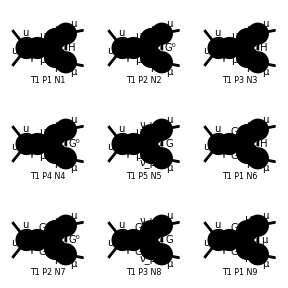

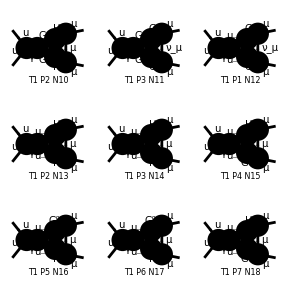

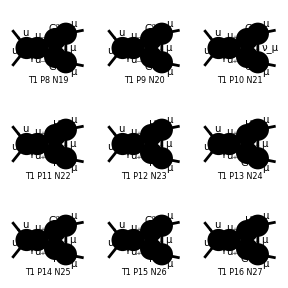

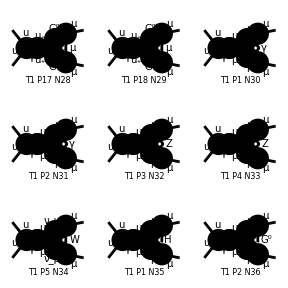

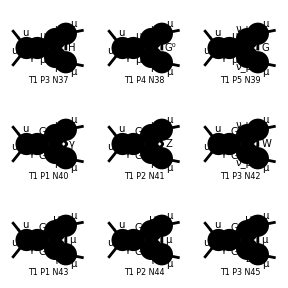

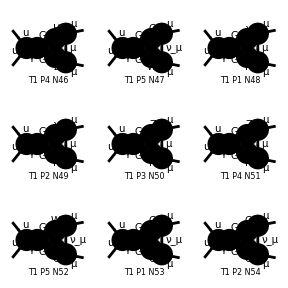

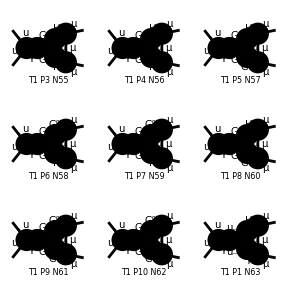

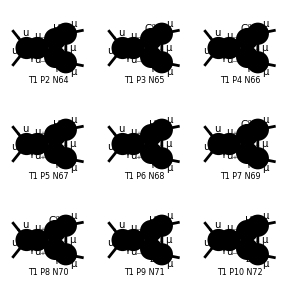

```mathematica
Paint[fields2LplanarnoT];
```

## Starting Input

## Lagrangian parameter replace

```mathematica
parameterReplace=<<(NotebookDirectory[]<>"smparameters.m");
chargeReplace={Ql->-1,I3l->-1/2,I3N->1/2,Qu->2/3,I3u->1/2,Qd->-1/3,I3d->-1/2};
cwReplace={cw->Sqrt[1-sw^2],mw->mz Sqrt[1-sw^2]};
complexReplace={mzC->mz,gZlLC->gZlL, gZlRC->gZlR, gZuLC->gZuL, gZuRC->gZuR};
```

Get::noopen: Cannot open \!\(\*RowBox[{"\"/home/riccardo/Documents/Fisica/Tesi/Processes/p-mm_2L_planar_massless_notr/ifdefinition/smparameters.m\""}]\).

## Functions

### Kira Propagator extraction

```mathematica
extractKiraProp[sm_]:=Module[{result,smtmp,kp,p},
smtmp=sm(*//Simplify*);
If[MatchQ[smtmp,PropList[p__]*expr_],
result=smtmp/.PropList[p__]*expr_->{p};
result=Times@@result;
];
If[!MatchQ[smtmp,PropList[p__]*expr_],
result=1;
];
Return[result]
];
```

```mathematica
extractMomenta[sm_]:=Module[{result,kpprod},
kpprod=extractKiraProp[sm];
If[kpprod===1, result={}];
If[Head[kpprod]===KiraPropagator, result=kpprod[[1]]];
If[Head[kpprod]===Times,
result=Map[#[[1]]&,List@@kpprod]
];
Return[result]
];
```

```mathematica
l=2;
ExtractFamily[sm[[l]]]
extractKiraProp[sm[[l]]]
```

{{False}}

KiraPropagator[q1,mm] KiraPropagator[p3+q1,mh] KiraPropagator[-p1-p2+p3+q1,mh] KiraPropagator[q2,mm] KiraPropagator[p1+p2+q2,mm] KiraPropagator[p3+q1+q2,mm]

### Analogous integral families

```mathematica
sameIntegral[ui1_userIntegral,ui2_userIntegral]:=Module[{if1,if2,test1,test2},
if1=ui1[[1]];
if2=ui2[[1]];
test1=userPropagatorMomenta[if1]^2-masses[ui1]^2;
test2=userPropagatorMomenta[if2]^2-masses[ui2]^2;
test1=test1^extractIndices[ui1];
test2=test2^extractIndices[ui2];
Return[test1===test2]
];
```

```mathematica
massIndex[mi_]:=ToExpression[StringDrop[ToString[mi],1]]
```

```mathematica
massSub[0,ui_userIntegral]:=0;
massSub[mi_,ui_userIntegral]:=ui[[2,massIndex[mi]]];
```

```mathematica
masses[ui_userIntegral]:=Module[{masses,massesReplace},
masses=Map[massSub[#,ui]&,userIntegralMasses[ui[[1]]]];
Return[masses]
];
```

```mathematica
extractIndices[ui_userIntegral]:=Delete[List@@ui,{{1},{2}}];
```

### Scalar integrals manipulation

```mathematica
si=<<(NotebookDirectory[]<>"scalar_integrals.m");
```

Get::noopen: Cannot open \!\(\*RowBox[{"\"/home/riccardo/Documents/Fisica/Tesi/Processes/p-mm_2L_planar_massless_notr/ifdefinition/scalar_integrals.m\""}]\).

```mathematica
mi=<<(NotebookDirectory[]<>"coefficients/Masters.m");
```

Get::noopen: Cannot open \!\(\*RowBox[{"\"/home/riccardo/Documents/Fisica/Tesi/Processes/p-mm_2L_planar_massless_notr/ifdefinition/coefficients/Masters.m\""}]\).

```mathematica
rules=<<(NotebookDirectory[]<>"kira_myintegrals.m");
```

Get::noopen: Cannot open \!\(\*RowBox[{"\"/home/riccardo/Documents/Fisica/Tesi/Processes/p-mm_2L_planar_massless_notr/ifdefinition/kira_myintegrals.m\""}]\).

```mathematica
substitution[si_userIntegral,rules_]:=Module[{result,rsi},
rsi=reduce[si];
result=rsi/.rules;
result=result/.massReplace[si];
Return[result];
]
```

```mathematica
substitute[si_userIntegral,rules_]:=Module[{result,m,mass,if,name,rsi},
m=si/.userIntegral[name_,mass_,x__]->mass;
if=si/.userIntegral[name_,mass_,x__]->name;
rsi=reduce[si];
result=rsi/.rules;
result=result/.massReplace[si];
Return[result];
]
```

```mathematica
masterReduction[si_userIntegral,rules_]:=Module[{result,m,mass,if,name,rsi,ifpattern,ifreplace},
m=si/.userIntegral[name_,mass_,x__]->mass;
if=si/.userIntegral[name_,mass_,x__]->name;
rsi=reduce[si];
result=rsi/.rules;
ifreplace=Map[#[x__]->userIntegral[#,DeleteCases[DeleteDuplicates[userIntegralMasses[#]],0],x]&,userIntegralFamiliesNames];
result=result/.ifreplace;
result=result/.massReplace[si];
Return[result];
]
```

```mathematica
reduce[si_userIntegral]:=Module[{result,name,x},
result=si/.userIntegral[name_,mass_,x__]->name[x];
Return[result]
]
```

```mathematica
massReplace[si_userIntegral]:=Module[{result,m,mass},
m=si/.userIntegral[name_,mass_,x__]->mass;
result=Array[(ToExpression[StringJoin["m",ToString[#]]]->m[[#]])&,Length[m]];
Return[result];
]
```

```mathematica
sectorList[si_List]:=Module[{result,l,x},
result=Array[0 &,9];
Do[
l=si[[i]]/.userIntegral[name_,mass_,x__]->{x};
Do[
If[l[[j]]>0,
result[[j]]=1
],
{j,Length[l]}]
,{i,Length[si]}];
Return[result]
]
```

```mathematica
si//sectorList
```

sectorList[$Failed]

```mathematica
si
```

$Failed

```mathematica
??Export
```

### Find r and s of UserIntegral lists

```mathematica
findR[si_List]:=Module[{rList,result},
rList=Map[sumPlus,si];
result=Max[rList];
Return[result]
];
```

```mathematica
findS[si_List]:=Module[{rList,result},
rList=Map[sumMinus,si];
result=Max[rList];
Return[result]
];
```

```mathematica
sumPlus[ui_userIntegral]:=Module[{indexList,result},
indexList=extractIndices[ui];
indexList=Map[positive,indexList];
result=Plus@@indexList;
Return[result]
];
```

```mathematica
sumMinus[ui_userIntegral]:=Module[{indexList,result},
indexList=-extractIndices[ui];
indexList=Map[positive,indexList];
result=Plus@@indexList;
Return[result]
];
```

```mathematica
positive[i_Integer]:=Module[{result},
If[i≥0,result=i];
If[i<0,result=0];
Return[result]
];
```

```mathematica
collectByIFname[si_List,name_]:=Module[{result},
result=DeleteDuplicates[Cases[si,userIntegral[name,___],Infinity]];
Return[result]
]
```

```mathematica
findActiveSectors[si_List]:=Module[{result,sectors,x},
result=ConstantArray[0,9];
Do[
sectors=si[[i]]/.userIntegral[_,_,x__]:>{x};
Do[
If[sectors[[j]]>0,result[[j]]=1]
,{j,Length[sectors]}]
,{i,Length[si]}];
Return[result]
]
```

### Scalar integrals manipulation

```mathematica
si=<<(NotebookDirectory[]<>"scalar_integrals.m");
```

Get::noopen: Cannot open \!\(\*RowBox[{"\"/home/riccardo/Documents/Fisica/Tesi/Processes/p-mm_2L_planar_massless_notr/ifdefinition/scalar_integrals.m\""}]\).

```mathematica
mi=<<(NotebookDirectory[]<>"coefficients/Masters.m");
```

Get::noopen: Cannot open \!\(\*RowBox[{"\"/home/riccardo/Documents/Fisica/Tesi/Processes/p-mm_2L_planar_massless_notr/ifdefinition/coefficients/Masters.m\""}]\).

```mathematica
rules=<<(NotebookDirectory[]<>"kira_myintegrals.m");
```

Get::noopen: Cannot open \!\(\*RowBox[{"\"/home/riccardo/Documents/Fisica/Tesi/Processes/p-mm_2L_planar_massless_notr/ifdefinition/kira_myintegrals.m\""}]\).

```mathematica
substitution[si_userIntegral,rules_]:=Module[{result,rsi},
rsi=reduce[si];
result=rsi/.rules;
result=result/.massReplace[si];
Return[result];
]
```

```mathematica
substitute[si_userIntegral,rules_]:=Module[{result,m,mass,if,name,rsi},
m=si/.userIntegral[name_,mass_,x__]->mass;
if=si/.userIntegral[name_,mass_,x__]->name;
rsi=reduce[si];
result=rsi/.rules;
result=result/.massReplace[si];
Return[result];
]
```

```mathematica
masterReduction[si_userIntegral,rules_]:=Module[{result,m,mass,if,name,rsi,ifpattern,ifreplace},
m=si/.userIntegral[name_,mass_,x__]->mass;
if=si/.userIntegral[name_,mass_,x__]->name;
rsi=reduce[si];
result=rsi/.rules;
ifreplace=Map[#[x__]->userIntegral[#,DeleteCases[DeleteDuplicates[userIntegralMasses[#]/.{M1->m1,M2->m2,M3->m3}],0],x]&,userIntegralFamiliesNames];
result=result/.ifreplace;
result=result/.massReplace[si];
Return[result];
]
```

```mathematica
reduce[si_userIntegral]:=Module[{result,name,x},
result=si/.userIntegral[name_,mass_,x__]->name[x];
Return[result]
]
```

```mathematica
massReplace[si_userIntegral]:=Module[{result,m,mass},
m=si/.userIntegral[name_,mass_,x__]->mass;
result=Array[(ToExpression[StringJoin["m",ToString[#]]]->m[[#]])&,Length[m]];
Return[result];
]
```

### Field Insertions manipulations

```mathematica
countInsertions[ins_]:=Module[{result,index},
result=0;
Do[
Do[
result+=Length[ins[[i,2,j,2]]];
,{j,Length[ins[[i,2]]]}];
,{i,Length[ins]}];
Return[result]
]
```

```mathematica
extractTopology[ins_Rule]:=ins[[1]];

extractLoopFields[top_]:=Module[{result},
result=Cases[top,Propagator[Loop[_]][Vertex[a1_][n1_],Vertex[a2_][n2_],f_]:>Rule[{n1,n2},f],Infinity]
]

extractLoopVertices[lines_]:=Module[{result},
result=Cases[lines,Rule[{n1_,n2_},f_]:>{n1,n2},Infinity]
]

next[{a_,b_},c_]:=Module[{result},
If[a=!=c && b=!=c,
result=c,
If[a===c,
result=b,
result=a
]
];
Return[result]
]

sortLoopFields[lines_List]:=Module[{result},
result=SortBy[lines,#[[2,1]]&]
]

triangles[top_]:=Module[{result,lines,vertices,a,b,c,verticesTmp,f1,f2,f3},
result={};
lines=extractLoopFields[top];
vertices=Map[Sort,extractLoopVertices[lines]];
Do[
a=vertices[[i,1]];
b=vertices[[i,2]];
verticesTmp=Delete[vertices,i];
Do[
If[!FreeQ[verticesTmp[[j]],a],
c=next[verticesTmp[[j]],a];
If[(!FreeQ[verticesTmp,Sort[{b,c}]]),
f1=Sort[{a,b}]/.lines;
f2=Sort[{a,c}]/.lines;
f3=Sort[{b,c}]/.lines;
result=AppendTo[result,sortLoopFields[{{Sort[{a,b}],f1},{Sort[{a,c}],f2},{Sort[{b,c}],f3}}]]
]
]
,{j,Length[verticesTmp]}]
,{i,Length[vertices]}];
Return[DeleteDuplicates[result]]
]

fermion[field_]:=Module[{result},
result=field;
If[MatchQ[field,-F[__]],
result=-field
];
Return[result]
]

deleteFermionTriangles[insertion_]:=Module[{result,n,diag,tri,rules,fields,check,deletelist},
n=countInsertions[insertion];
deletelist={};
Do[
diag=DiagramExtract[insertion,i];
tri=triangles[diag[[1,1]]];
rules=List@@diag[[1,2,1,2,1]];
If[tri=!={},
Do[
fields=Map[fermion[#[[2]]]&,tri[[j]]/.rules];
If[MatchQ[fields,{F[__],F[__],F[__]}]||MatchQ[fields,{-F[__],-F[__],-F[__]}],
deletelist=AppendTo[deletelist,i]
]
,{j,Length[tri]}]
]
,{i,n}];
deletelist=DeleteDuplicates[deletelist];
result=DiagramDelete[insertion,deletelist];
Return[result]
]
```

```mathematica
deleteFermionTriangles[fields2Lplanar]
```

TopologyList[Process→{F[3,{1,o}],-F[3,{1,o}]}→{F[2,{2}],-F[2,{2}]},Model→{SMbgf_Anglerfish},GenericModel→{Lorentzbgf},InsertionLevel→{Particles},ExcludeParticles→{},ExcludeFieldPoints→{},LastSelections→{}][Topology[1][Propagator[Incoming][Vertex[1][1],Vertex[3][5],Field[1]],Propagator[Incoming][Vertex[1][2],Vertex[3][5],Field[2]],7,Propagator[Loop[1]][Vertex[3][-2],Vertex[3][7],Field[10]],Propagator[Loop[1]][Vertex[3][-2],Vertex[3][8],Field[11]]]→Insertions[Generic][1],1]
 |  |  |  |

### Coefficient Manipulation

```mathematica
notNull[x_]:=Module[{result},
If[x===0,result=0,result=1];
Return[result]
]
contributions[coefflist_List]:=Module[{result},
If[MatrixQ[coefflist],
result=Map[notNull,coefflist,{2}];
Return[result]
,
Message[contributions::nomatrix,"Argument is not a matrix"];
Return[Null]
]
]
```

### Loop Checking

```mathematica
checkLoop[ins_,n_Integer]:=Module[{result},
result=!FreeQ[loopOrderList[ins],Centre[n]];
Return[result]
]
```

```mathematica
loopOrderList[ins_]:=Module[{result,n},
result=DeleteDuplicates[Cases[ToTree[ins[[1,1]]],Centre[n_][_]:>Centre[n],Infinity]];
Return[result]
]
```

### Contribution

```mathematica
contr[masters_List,coefficients_List]:=Module[{result},
If[Length[masters]===Length[coefficients],
result=Plus@@(masters*coefficients),
Message[contr::nomatrix,"Number of Masters different from number of coefficients"];
Return[Null]
];
Return[result]
]
```

### Sum of contributions

```mathematica
totContr[ndig_,nmas_,bornIndex_]:=Module[{result},
result=diagramCoefficients[[bornIndex,ndig,nmas]];
(*result=diagramCoefficientsRep[[ndig,1,nmas]]+diagramCoefficientsRep[[ndig,2,nmas]];*)
Return[result]
]
```

```mathematica
sumContr[nlist_List,nmas_,bornIndex_]:=Module[{result},
result=Simplify[Sum[totContr[nlist[[i]],nmas,bornIndex],{i,Length[nlist]}]];
Return[result]
]
```

```mathematica
totContrRep[ndig_,nmas_,bornIndex_]:=Module[{result},
result=diagramCoefficientsRep[[bornIndex,ndig,nmas]];
result=diagramCoefficientsRep[[ndig,1,nmas]]+diagramCoefficientsRep[[ndig,2,nmas]];
Return[result]
]
```

```mathematica
sumContrRep[nlist_List,nmas_,bornIndex_]:=Module[{result},
result=Simplify[Sum[totContrRep[bornIndex,nlist[[i]],nmas],{i,Length[nlist]}]];
Return[result]
]
```